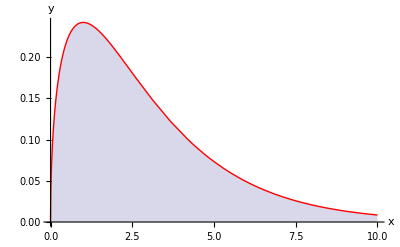

```mathematica
Needs["PlotLegends`"];
Ct=Evaluate@Table[PDF[ChiSquareDistribution[q],x],{q,{3}}];
Ct2=Evaluate@Table[PDF[ChiSquareDistribution[w],z],{w,{3}}];
figure=Plot[
{Ct,Ct2},
{x,0,10},
PlotPoints->20,
PlotStyle->{Red},
Filling->Axis,
AxesOrigin->{0,0},
AxesLabel->{x,y},
PlotLegend->{"ChiQuadro" },
LegendSize->{0.35,0.15},
LegendPosition->{0.5,-0.4},
LegendShadow->{0,0}
]
Export["/home/federico/workspace/books/imadls/mathematica/chiquadrotest.eps",figure,"EPS"];
```